Construction of the phantom.(According to Bronnikov)
The real part of the refractive index is written as : n (x1, x2, x3) = 1 + f (x1, x2, x3).The wavelength λ is measured in μm :

```mathematica
λ=0.1 10^-3;
```

Construction of one spherical phantom to compose a phantom of spherical objects.

```mathematica
spherefunc[{x1_,x2_,x3_},{o1_,o2_,o3_},amp_,dia_]:=
amp Boole[(x1-o1)^2+(x2-o2)^2+(x3-o3)^2≤(dia/2)^2]
```

Plot of cross sections of the sphere function

1.15207

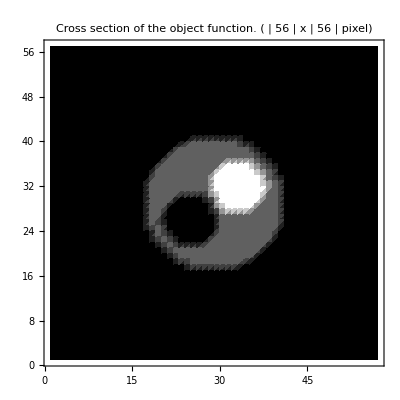

```mathematica
Clear[crossplot];
crossplot[dia_,n_,range_,phi_,y_]:=Block[{vec,sphere1,sphere2,sphere3,n1,n2,plot},

vec=Evaluate[
{{Cos[phi],-Sin[phi],0},{Sin[phi],Cos[phi],0},{0,0,1}}.{ range(-1/2+n1/n),y ,range(-1/2+n2/n)}];
sphere1=spherefunc[vec,{0,0,0},-3 *10^-7 ,dia];
sphere2=spherefunc[vec,dia/4.5{1,1,1}/Sqrt[3],-5*10^-7 ,dia/2.5];
sphere3=spherefunc[vec,-dia/4.5{1,1,1}/Sqrt[3],3 *10^-7,dia/2.5];

Print[
Timing[
plot=ListDensityPlot[
 Table[-(sphere1+sphere2+sphere3),{n2,0,n},{n1,0,n}],
ColorFunction->GrayLevel,PlotLabel->TableForm[{{"Cross section of the object function. (",n,"x",n,"pixel)"}}]
]
][[1]]
];
plot
];
crossplot[108,56,256,π/4,0]
```

The wave field downstream  of the object is u[x, y, θ] = Exp[i phase[x, y, θ] - μ[x, y, θ]/2]. Assuming μ = 0 it is given by

```mathematica
Clear[int];
int[{x_,y_},{o1_,o2_,o3_},θ_,amp_,dia_,range_:128]:=Block[{sub,xint,x1,x2,sphere},

sub=N@If[θ≠π/2,xint=x2;Solve[x-x1 Cos[θ]-x2 Sin[θ]==0,x1],xint=x1;Solve[x-x1 Cos[θ]-x2 Sin[θ]==0,x2]][[1]];

sphere=spherefunc[{x1,x2,y},{o1,o2,o3},amp,dia]/.sub;

Integrate[sphere,{xint,-range/2,range/2}]

];
```

Plots of the downstream

```mathematica
Clear[phase];
phase[dia_,size_,padmult_]:=Block[{ob,x,y},

ob=-2*10^-7
+int[{x,y},{0,0,0},π/4,-3*10^-7,dia,padmult size]
+int[{x,y},dia/4.5{1,1,1}/Sqrt[3],π/4,-5*10^-7 ,dia/2.5,padmult size]
+int[{x,y},-dia/4.5{1,1,1}/Sqrt[3],π/4,3*10^-7,dia/2.5,padmult size];

2π /λ Table[ob,{x,-padmult size/2,padmult size/2,padmult},{y,-padmult size/2,padmult size/2,padmult}]

]
```

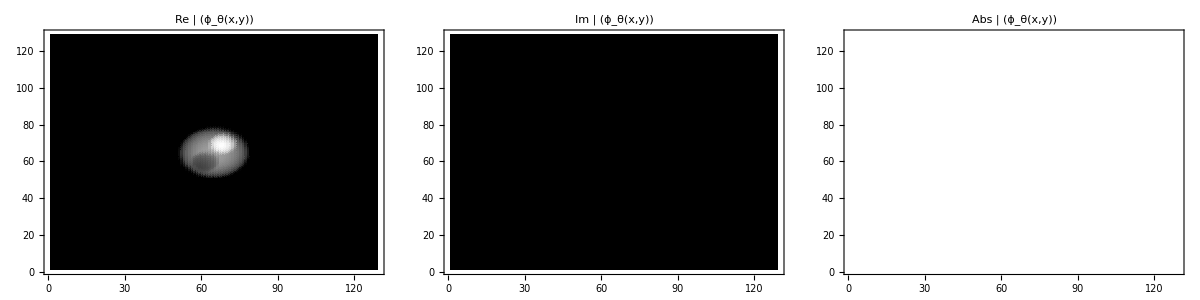
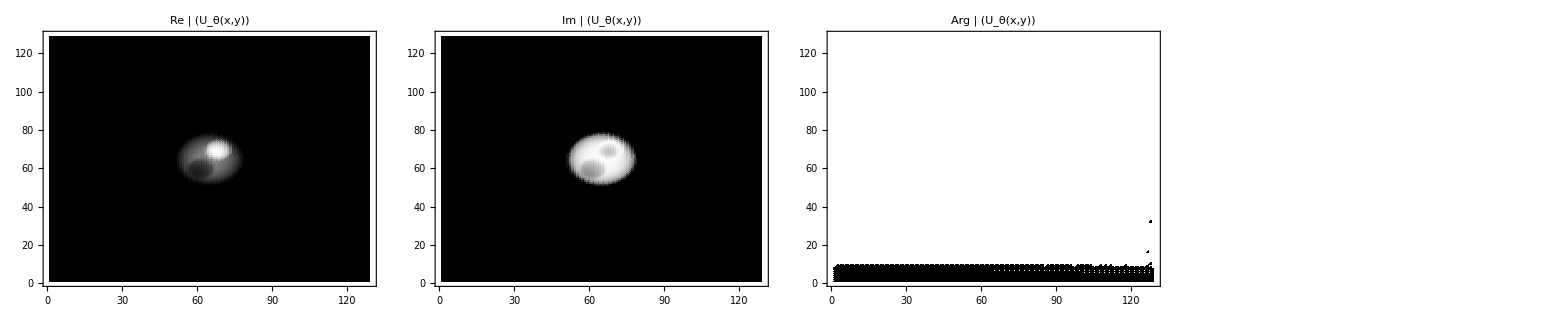

```mathematica
Block[{plist},

plist=phase[108,128,4];
TableForm[{
TableForm@{Table[ListDensityPlot[-head@plist,ColorFunction->GrayLevel,PlotLabel->TableForm[{{head,"(ϕ_θ(x,y))"}}]],{head,{Re,Im,Abs}}]},
TableForm@{Table[ListDensityPlot[-head@Exp[ⅈ plist],ColorFunction->GrayLevel,PlotLabel->TableForm[{{head,"(U_θ(x,y))"}}]],{head,{Re,Im,Arg,Abs}}]}
}]

]
```

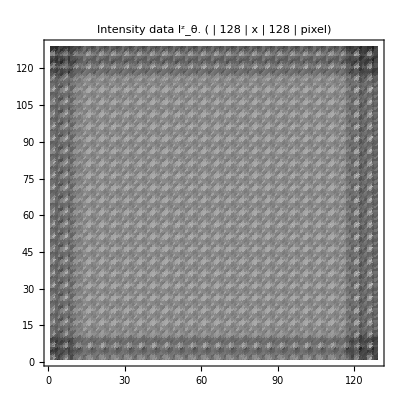

```mathematica
Module[{size=128,padmult=4,dist=20 10^4,inv,intlist},

inv=InverseFourier[
Fourier[Exp[ⅈ 2π /λ phase[108,size,padmult]]]*Fourier[Table[Exp[(ⅈ π)/(λ dist)(n^2+m^2)],{n,-padmult size/2,padmult size/2,padmult},{m,-padmult size/2,padmult size/2,padmult}]]
];

intlist=(Abs@Transpose@RotateRight[Transpose@RotateRight[inv,size/2],size/2])^2;

ListDensityPlot[intlist,ColorFunction->GrayLevel,PlotLabel->TableForm[{{"Intensity data (I^z)_θ. (",size,"x",size,"pixel)"}}]]
]
```